```mathematica
dim = 64;
lattice = RandomReal[{-1.5, 1.5}, {dim, dim}];
```

```mathematica
magnetization[lattice_]:=Total[lattice,2]/dim^2
p = Join[Range[0, dim/2-1],Range[-dim/2+1,0]];
p2= Outer[#1^2 + #2^2 &, p, p];
ρ[τ_]:=Map[Re, InverseFourier[ⅇ^(-p2*τ) * Fourier[lattice]], {2}]
```

```mathematica
Plot[magnetization[ρ[τ]],{τ,0,1}]
```

-Graphics-

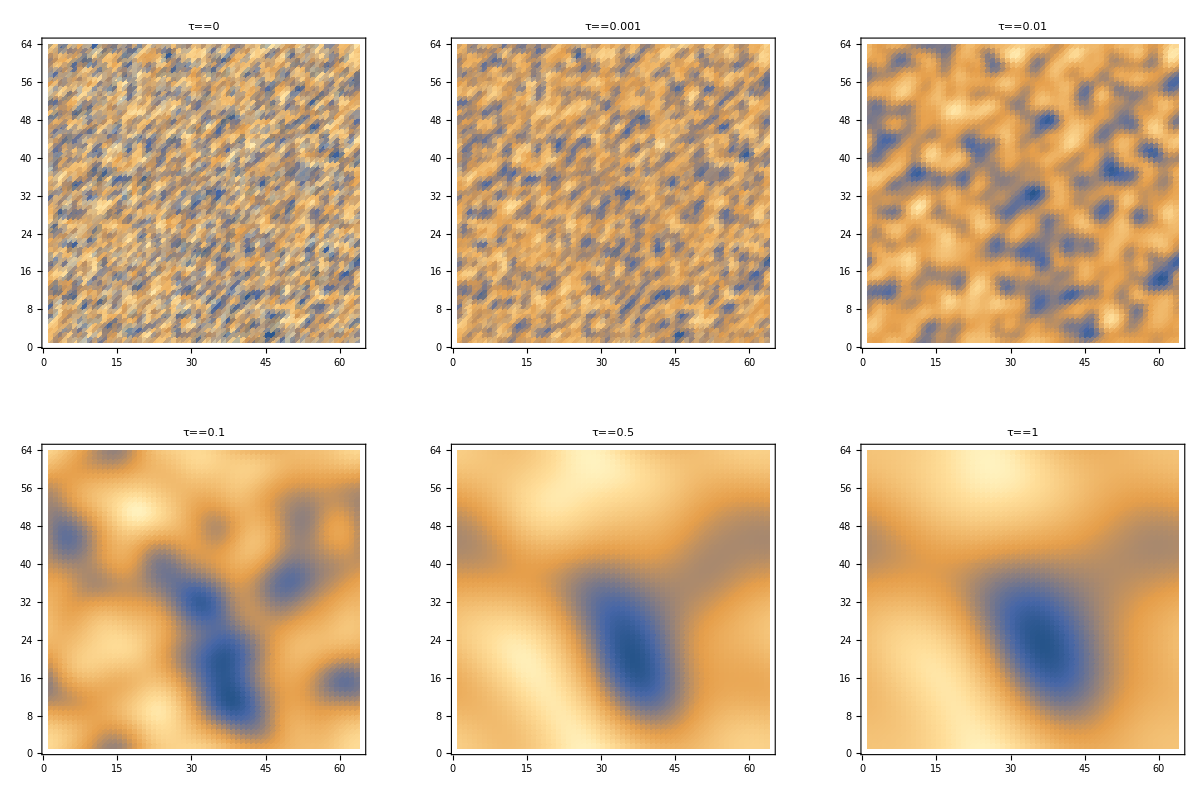

```mathematica
taus = {0,0.001, 0.01, 0.1, 0.5, 1};GraphicsGrid[ArrayReshape[Map[ListDensityPlot[ρ[#1], PlotLabel-> τ==#1] &, taus], {2, Length[taus]/2}]]
```